```mathematica
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
PolarizationSum[x_,y_,z_,s_,v_]:=1/2(PolarizationSum[x,z,v]PolarizationSum[y,s,v]+PolarizationSum[x,s,v]PolarizationSum[y,z,v])-1/3 PolarizationSum[x,y,v]PolarizationSum[z,s,v]
PolarizationSum[x_,y_,z_,a_,b_,c_,v_]:=-1/15((PolarizationSum[x,z,v]*PolarizationSum[b,y,v]+PolarizationSum[x,b,v]*PolarizationSum[z,y,v]+PolarizationSum[x,y,v]*PolarizationSum[z,b,v])*PolarizationSum[a,c,v]+
(PolarizationSum[x,z,v]*PolarizationSum[b,a,v]+PolarizationSum[x,b,v]*PolarizationSum[z,a,v]+PolarizationSum[x,a,v]*PolarizationSum[z,b,v])*PolarizationSum[y,c,v]+(PolarizationSum[x,z,v]*PolarizationSum[b,c,v]+PolarizationSum[x,b,v]*PolarizationSum[z,c,v]+PolarizationSum[x,c,v]*PolarizationSum[z,b,v])*PolarizationSum[y,a,v])+1/6((PolarizationSum[x,y,v]*PolarizationSum[z,a,v]+PolarizationSum[x,a,v]*PolarizationSum[y,z,v])*PolarizationSum[b,c,v]+(PolarizationSum[x,a,v]*PolarizationSum[z,c,v]+PolarizationSum[x,c,v]*PolarizationSum[a,z,v])*PolarizationSum[b,y,v]+(PolarizationSum[x,y,v]*PolarizationSum[z,c,v]+PolarizationSum[x,c,v]*PolarizationSum[y,z,v])*PolarizationSum[b,a,v])
```

```mathematica
qvec[mIn_,mOut_,mPi_]:=(√((mIn^2-(mOut+mPi)^2)(mIn^2-(mOut-mPi)^2)))/(2mIn)
```

```mathematica
ScalarProduct[v,v]=1;
ScalarProduct[q,q]=mPi^2;
ScalarProduct[v,q]=√(mPi^2+qvec^2);
```

```mathematica
SetAttributes[G,HoldAll]
```

```mathematica
NotSymbolQ[expr_Symbol]:=False
NotSymbolQ[expr_]:=True
Err[expr_?NotSymbolQ]:=√Total[D[expr,#]^2 Err[#]^2&/@ Variables[expr]]
```

```mathematica
massRules ={
mD2sN->3214.0,
Err[mD2sN]->√(29.0^2+33.0^2+36.0^2),
mDS2s->3214.0+99.02,
Err[mDS2s]->√(29.0^2+33.0^2+36.0^2+24.64^2),
mDN->1864.83,
Err[mDN]->0.05,
mDC->1869.59,
Err[mDC]->0.09,
mDsN->2006.85,
Err[mDsN]->0.05,
mDsC->2010.26,
Err[mDsC]->0.05,
mDSC->1968.28,
Err[mDSC]->0.10,
mDSsC->2112.1,
Err[mDSsC]->0.4,
mPiN->134.977,
Err[mPiN]->0.0005,
mPiC->139.57061,
Err[mPiC]->0.00024,
mKN->497.611,
Err[mKN]->0.013,
mKC->493.677,
Err[mKC]->0.016,
mEta->547.862,
Err[mEta]->0.017
};
```

## H = (P, Ps)

## P ⟶Ps Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M[mu_]:=gTR[(√mPs GA[mu]).((1+GS[v])/2).(√mP GA[5]).(1/fPi GS[q]).GA[5]]
```

```mathematica
Amp = M[mu]ComplexConjugate[M[nu]]PolarizationSum[mu,nu,v]//Contract
```

(4 g^2 mP mPs (mPi^2+qvec^2))/fPi^2-(4 g^2 mP mPi^2 mPs)/fPi^2

```mathematica
G[P,Ps]=1/(8 π)Amp qvec/mP^2//Simplify
```

(g^2 mPs qvec^3)/(2 π fPi^2 mP)

## Ps ⟶P Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M[mu_]:=g TR[(√mP GA[5]).((1+GS[v])/2).(√mPs GA[mu]).(1/fPi GS[q]).GA[5]]
```

```mathematica
Amp =1/3 M[mu]ComplexConjugate[M[nu]]PolarizationSum[mu,nu,v]//Contract
```

(4 g^2 mP mPs (mPi^2+qvec^2))/(3 fPi^2)-(4 g^2 mP mPi^2 mPs)/(3 fPi^2)

```mathematica
G[Ps,P]=1/(8 π)Amp qvec/mPs^2//Simplify
```

(g^2 mP qvec^3)/(6 π fPi^2 mPs)

## Pst ⟶Ps Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M[mu_,nu_]:=g TR[(√mPs GA[nu]).((1+GS[v])/2).(√mPst GA[mu]).(1/fPi GS[q]).GA[5]]
```

```mathematica
Amp =1/3 M[mu,rho]ComplexConjugate[M[nu,sigma]]PolarizationSum[mu,nu,v]PolarizationSum[rho,sigma,v]//Contract
```

(8 g^2 mPs mPst qvec^2)/(3 fPi^2)

```mathematica
G[Pst,Ps]=1/(8 π)Amp qvec/mPst^2//Simplify
```

(g^2 mPs qvec^3)/(3 π fPi^2 mPst)

## S = (P0s, Psp)

## P0s ⟶P Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M:=gTR[(√mP GA[5]).((1+GS[v])/2).(√mP0s).(1/fPi GS[q]).GA[5]]
```

```mathematica
Amp = M ComplexConjugate[M]
```

(4 g^2 mP mP0s (mPi^2+qvec^2))/fPi^2

```mathematica
G[P0s,P]=1/(8 π)Amp qvec/mP0s^2//Simplify
```

(g^2 mP qvec (mPi^2+qvec^2))/(2 π fPi^2 mP0s)

## Psp ⟶Ps Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M[mu_,nu_]:=g TR[(√mPs GA[nu]).((1+GS[v])/2).(√mPsp GA[mu].GA[5]).(1/fPi GS[q]).GA[5]]
```

```mathematica
Amp =1/3 M[mu,rho]ComplexConjugate[M[nu,sigma]]PolarizationSum[mu,nu,v]PolarizationSum[rho,sigma,v]//Contract
```

(4 g^2 mPs mPsp (mPi^2+qvec^2))/fPi^2

```mathematica
G[Psp,Ps]=1/(8 π)Amp qvec/mPsp^2//Simplify
```

(g^2 mPs qvec (mPi^2+qvec^2))/(2 π fPi^2 mPsp)

## T = (P1, P2s)

## P1⟶Ps Pi

```mathematica
ClearAll[P1,M,Amp]
```

```mathematica
P1[mu_,nu_]:=√mP1 √(3/2)GA[5].(MT[mu,nu]- 1/3 GA[nu].(GA[mu]-FV[v,mu]))
```

```mathematica
M[mu_,nu_]:=hp/lambdaChi TR[(√mPs GA[nu]).((1+GS[v])/2).P1[indx`rho,mu].(2/fPi FV[q,indx`rho]GS[q]).GA[5]]
```

```mathematica
Amp=1/3 M[mu,nu]ComplexConjugate[M[alpha,beta]]PolarizationSum[mu,alpha,v]PolarizationSum[nu,beta,v]//Contract
```

(8 hp^2 mP1 mPi^4 mPs)/(fPi^2 lambdaChi^2)+(16 hp^2 mP1 mPi^2 mPs qvec^2)/(3 fPi^2 lambdaChi^2)-(16 hp^2 mP1 mPi^2 mPs (mPi^2+qvec^2))/(fPi^2 lambdaChi^2)+(8 hp^2 mP1 mPs (mPi^2+qvec^2)^2)/(fPi^2 lambdaChi^2)-(16 hp^2 mP1 mPs qvec^2 (mPi^2+qvec^2))/(3 fPi^2 lambdaChi^2)+(8 hp^2 mP1 mPs qvec^4)/(3 fPi^2 lambdaChi^2)

```mathematica
G[P1,Ps]=1/(8 π)Amp qvec/mP1^2//Simplify
```

(2 hp^2 mPs qvec^5)/(3 π fPi^2 lambdaChi^2 mP1)

## P2s⟶P Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M[mu_,nu_]:=hp/lambdaChi TR[(√mP GA[5]).((1+GS[v])/2).(√mP2s GA[nu]).(2/fPi FV[q,mu]GS[q]).GA[5]]
```

```mathematica
Amp=1/5 M[mu,nu]ComplexConjugate[M[alpha,beta]]PolarizationSum[mu,nu,alpha,beta,v]//Contract
```

(32 hp^2 mP mP2s mPi^4)/(15 fPi^2 lambdaChi^2)-(64 hp^2 mP mP2s mPi^2 (mPi^2+qvec^2))/(15 fPi^2 lambdaChi^2)+(32 hp^2 mP mP2s (mPi^2+qvec^2)^2)/(15 fPi^2 lambdaChi^2)

```mathematica
G[P2s,P]=1/(8 π)Amp qvec/mP2s^2//Simplify
```

(4 hp^2 mP qvec^5)/(15 π fPi^2 lambdaChi^2 mP2s)

## P2s⟶Ps Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M[mu_,nu_,rho_]:=hp/lambdaChi TR[(√mPs GA[rho]).((1+GS[v])/2).(√mP2s GA[nu]).(2/fPi FV[q,mu]GS[q]).GA[5]]
```

```mathematica
Amp=1/5 M[mu,nu,rho]ComplexConjugate[M[alpha,beta,sigma]]PolarizationSum[mu,nu,alpha,beta,v]PolarizationSum[rho,sigma]//Contract
```

2 qvec^2 ((8 hp^2 mP2s mPi^2 mPs)/(5 fPi^2 lambdaChi^2)+(8 hp^2 mP2s mPs qvec^2)/(5 fPi^2 lambdaChi^2))-(16 hp^2 mP2s mPi^2 mPs qvec^2)/(5 fPi^2 lambdaChi^2)

```mathematica
G[P2s,Ps]=1/(8 π)Amp qvec/mP2s^2//Simplify
```

(2 hp^2 mPs qvec^5)/(5 π fPi^2 lambdaChi^2 mP2s)

## X = (P1s, P2)

## P1s⟶P Pi

```mathematica
ClearAll[P1s,M, Amp]
```

```mathematica
P1s[mu_,nu_]:=√mP1s √(3/2)(MT[mu,nu]- 1/3 GA[nu].(GA[mu]+FV[v,mu]))
```

```mathematica
M[mu_]:=kp/lambdaChi TR[(√mP GA[5]).((1+GS[v])/2).P1s[indx`nu,mu].(2/fPi FV[q,indx`nu]GS[q]).GA[5]]
```

```mathematica
Amp = 1/3 M[mu]ComplexConjugate[M[nu]]PolarizationSum[mu,nu,v]//Contract
```

(32 kp^2 mP mP1s (mPi^2+qvec^2)^2)/(9 fPi^2 lambdaChi^2)-(32 kp^2 mP mP1s mPi^2 (mPi^2+qvec^2))/(9 fPi^2 lambdaChi^2)

```mathematica
G[P1s,P]=1/(8 π)Amp qvec/mP1s^2//Simplify
```

(4 kp^2 mP qvec^3 (mPi^2+qvec^2))/(9 π fPi^2 lambdaChi^2 mP1s)

## P1s⟶Ps Pi

```mathematica
ClearAll[P1s,M, Amp]
```

```mathematica
P1s[mu_,nu_]:=√mP1s √(3/2)(MT[mu,nu]- 1/3 GA[nu].(GA[mu]+FV[v,mu]))
```

```mathematica
M[mu_,nu_]:=kp/lambdaChi TR[(√mPs GA[nu]).((1+GS[v])/2).P1s[indx`nu,mu].(2/fPi FV[q,indx`nu]GS[q]).GA[5]]
```

```mathematica
Amp = 1/3 M[mu,alpha]ComplexConjugate[M[nu,beta]]PolarizationSum[mu,nu,v]PolarizationSum[alpha,beta,v]//Contract
```

2 qvec^2 ((8 kp^2 mP1s mPi^2 mPs)/(9 fPi^2 lambdaChi^2)+(8 kp^2 mP1s mPs qvec^2)/(9 fPi^2 lambdaChi^2))

```mathematica
G[P1s,Ps]=1/(8 π)Amp qvec/mP1s^2//Simplify
```

(2 kp^2 mPs qvec^3 (mPi^2+qvec^2))/(9 π fPi^2 lambdaChi^2 mP1s)

## P2⟶Ps Pi

```mathematica
ClearAll[M, Amp]
```

```mathematica
M[mu_,nu_,rho_]:=kp/lambdaChi TR[(√mPs GA[rho]).((1+GS[v])/2).(√mP2 GA[5].GA[nu]).(2/fPi FV[q,mu]GS[q]).GA[5]]
```

```mathematica
Amp = 1/5 M[mu,nu,alpha]ComplexConjugate[M[rho,sigma,beta]]PolarizationSum[mu,nu,rho,sigma,v]PolarizationSum[alpha,beta,v]//Contract
```

(16 kp^2 mP2 mPs (mPi^2+qvec^2)^2)/(3 fPi^2 lambdaChi^2)-(16 kp^2 mP2 mPi^2 mPs (mPi^2+qvec^2))/(3 fPi^2 lambdaChi^2)

```mathematica
G[P2,Ps ]=1/(8 π)Amp qvec/mP2^2//Simplify
```

(2 kp^2 mPs qvec^3 (mPi^2+qvec^2))/(3 π fPi^2 lambdaChi^2 mP2)

## X’ = (P2p, P3s)

## P2p⟶Ps Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
P2p[mu_,nu_,alpha_,beta_]:=√mP2p √(5/3)GA[5].(MT[mu,alpha]MT[nu,beta]- 1/5 MT[nu,beta]GA[alpha].(GA[mu]-FV[v,mu])- 1/5 MT[mu,alpha]GA[beta].(GA[nu]-FV[v,nu]))
```

```mathematica
M[mu_,nu_,rho_]:=k/lambdaChi^2 TR[(√mPs GA[rho]).((1+GS[v])/2).P2p[indx`mu,indx`nu,mu,nu].(2/fPi FV[q,indx`mu]FV[q,indx`nu]GS[q]).GA[5]]
```

```mathematica
Amp = 1/5 M[mu,nu,alpha]ComplexConjugate[M[rho,sigma,beta]]PolarizationSum[mu,nu,rho,sigma,v]PolarizationSum[alpha,beta,v]//Contract
```

-(32 k^2 mP2p mPi^6 mPs)/(9 fPi^2 lambdaChi^4)-(128 k^2 mP2p mPi^4 mPs qvec^2)/(45 fPi^2 lambdaChi^4)-(64 k^2 mP2p mPi^2 mPs qvec^4)/(45 fPi^2 lambdaChi^4)-(32 k^2 mP2p mPi^2 mPs (mPi^2+qvec^2)^2)/(3 fPi^2 lambdaChi^4)+(256 k^2 mP2p mPi^2 mPs qvec^2 (mPi^2+qvec^2))/(45 fPi^2 lambdaChi^4)+(32 k^2 mP2p mPs (mPi^2+qvec^2)^3)/(9 fPi^2 lambdaChi^4)-(128 k^2 mP2p mPs qvec^2 (mPi^2+qvec^2)^2)/(45 fPi^2 lambdaChi^4)+(64 k^2 mP2p mPs qvec^4 (mPi^2+qvec^2))/(45 fPi^2 lambdaChi^4)+(32 k^2 mP2p mPi^4 mPs (mPi^2+qvec^2))/(3 fPi^2 lambdaChi^4)

```mathematica
G[P2p,Ps]=1/(8 π)Amp qvec/mP2p^2//Simplify
```

(4 k^2 mPs qvec^7)/(15 π fPi^2 lambdaChi^4 mP2p)

## P3s⟶P Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M[mu_,nu_,rho_]:=k/lambdaChi^2 TR[(√mP GA[5]).((1+GS[v])/2).(√mP3s GA[rho]).(2/fPi FV[q,mu]FV[q,nu]GS[q]).GA[5]]
```

```mathematica
Amp = 1/7 M[mu,nu,alpha]ComplexConjugate[M[rho,sigma,beta]]PolarizationSum[mu,nu,alpha,rho,sigma,beta,v]//Contract
```

-(32 k^2 mP mP3s mPi^6)/(35 fPi^2 lambdaChi^4)-(96 k^2 mP mP3s mPi^2 (mPi^2+qvec^2)^2)/(35 fPi^2 lambdaChi^4)+(32 k^2 mP mP3s (mPi^2+qvec^2)^3)/(35 fPi^2 lambdaChi^4)+(96 k^2 mP mP3s mPi^4 (mPi^2+qvec^2))/(35 fPi^2 lambdaChi^4)

```mathematica
G[P3s,P ]=1/(8 π)Amp qvec/mP3s^2//Simplify
```

(4 k^2 mP qvec^7)/(35 π fPi^2 lambdaChi^4 mP3s)

## P3s⟶Ps Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M[mu_,nu_,rho_,sigma_]:=k/lambdaChi^2 TR[(√mPs GA[sigma]).((1+GS[v])/2).(√mP3s GA[rho]).(2/fPi FV[q,mu]FV[q,nu]GS[q]).GA[5]]
```

```mathematica
Amp = 1/7 M[mu,nu,alpha,eta]ComplexConjugate[M[rho,sigma,beta,lambda]]PolarizationSum[mu,nu,alpha,rho,sigma,beta,v]PolarizationSum[eta,lambda]//Contract
```

(128 k^2 mP3s mPi^4 mPs qvec^2)/(105 fPi^2 lambdaChi^4)+8 qvec^2 (-(8 k^2 mP3s mPi^4 mPs)/(21 fPi^2 lambdaChi^4)-(8 k^2 mP3s mPi^2 mPs qvec^2)/(21 fPi^2 lambdaChi^4))+4 qvec^2 ((16 k^2 mP3s mPi^4 mPs)/(105 fPi^2 lambdaChi^4)+(16 k^2 mP3s mPi^2 mPs qvec^2)/(105 fPi^2 lambdaChi^4))+2 qvec^2 ((64 k^2 mP3s mPi^4 mPs)/(105 fPi^2 lambdaChi^4)+(128 k^2 mP3s mPi^2 mPs qvec^2)/(105 fPi^2 lambdaChi^4)+(64 k^2 mP3s mPs qvec^4)/(105 fPi^2 lambdaChi^4))

```mathematica
G[P3s,Ps]=1/(8 π)Amp qvec/mP3s^2//Simplify
```

(16 k^2 mPs qvec^7)/(105 π fPi^2 lambdaChi^4 mP3s)

## F = (P2sp, P3)

## P2sp⟶P Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
P2sp[mu_,nu_,alpha_,beta_]:=√mP2sp √(5/3)(MT[mu,alpha]MT[nu,beta]- 1/5 MT[nu,beta]GA[alpha].(GA[mu]+FV[v,mu])- 1/5 MT[mu,alpha]GA[beta].(GA[nu]+FV[v,nu]))
```

```mathematica
M[mu_,nu_]:=l/lambdaChi^2 TR[(√mP GA[5]).((1+GS[v])/2).P2sp[indx`mu,indx`nu,mu,nu].(2/fPi FV[q,indx`mu]FV[q,indx`nu]GS[q]).GA[5]]
```

```mathematica
Amp = 1/5 M[mu,nu]ComplexConjugate[M[rho,sigma]]PolarizationSum[mu,nu,rho,sigma,v]//Contract
```

-(64 l^2 mP mP2sp mPi^2 (mPi^2+qvec^2)^2)/(25 fPi^2 lambdaChi^4)+(32 l^2 mP mP2sp (mPi^2+qvec^2)^3)/(25 fPi^2 lambdaChi^4)+(32 l^2 mP mP2sp mPi^4 (mPi^2+qvec^2))/(25 fPi^2 lambdaChi^4)

```mathematica
G[P2sp,P ]=1/(8 π)Amp qvec/mP2sp^2//Simplify
```

(4 l^2 mP qvec^5 (mPi^2+qvec^2))/(25 π fPi^2 lambdaChi^4 mP2sp)

## P2sp⟶Ps Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
P2sp[mu_,nu_,alpha_,beta_]:=√mP2sp √(5/3)(MT[mu,alpha]MT[nu,beta]- 1/5 MT[nu,beta]GA[alpha].(GA[mu]+FV[v,mu])- 1/5 MT[mu,alpha]GA[beta].(GA[nu]+FV[v,nu]))
```

```mathematica
M[mu_,nu_,rho_]:=l/lambdaChi^2 TR[(√mPs GA[rho]).((1+GS[v])/2).P2sp[indx`mu,indx`nu,mu,nu].(2/fPi FV[q,indx`mu]FV[q,indx`nu]GS[q]).GA[5]]
```

```mathematica
Amp = 1/5 M[mu,nu,alpha]ComplexConjugate[M[rho,sigma,beta]]PolarizationSum[mu,nu,rho,sigma,v]PolarizationSum[alpha,beta,v]//Contract
```

8 qvec^2 (-(8 l^2 mP2sp mPi^4 mPs)/(75 fPi^2 lambdaChi^4)-(8 l^2 mP2sp mPi^2 mPs qvec^2)/(75 fPi^2 lambdaChi^4))+8 qvec^2 ((8 l^2 mP2sp mPi^4 mPs)/(75 fPi^2 lambdaChi^4)+(16 l^2 mP2sp mPi^2 mPs qvec^2)/(75 fPi^2 lambdaChi^4)+(8 l^2 mP2sp mPs qvec^4)/(75 fPi^2 lambdaChi^4))

```mathematica
G[P2sp,Ps]=1/(8 π)Amp qvec/mP2sp^2//Simplify
```

(8 l^2 mPs qvec^5 (mPi^2+qvec^2))/(75 π fPi^2 lambdaChi^4 mP2sp)

## P3⟶Ps Pi

```mathematica
ClearAll[M,Amp]
```

```mathematica
M[mu_,nu_,rho_,sigma_]:=l/lambdaChi^2 TR[(√mPs GA[sigma]).((1+GS[v])/2).(√mP3 GA[rho].GA[5]).(2/fPi FV[q,mu]FV[q,nu]GS[q]).GA[5]]
```

```mathematica
Amp = 1/7 M[mu,nu,alpha,eta]ComplexConjugate[M[rho,sigma,beta,lambda]]PolarizationSum[mu,nu,alpha,rho,sigma,beta,v]PolarizationSum[eta,lambda]//Contract
```

(32 l^2 mP3 mPi^6 mPs)/(35 fPi^2 lambdaChi^4)-(32 l^2 mP3 mPi^2 mPs (mPi^2+qvec^2)^2)/(21 fPi^2 lambdaChi^4)+(128 l^2 mP3 mPs (mPi^2+qvec^2)^3)/(105 fPi^2 lambdaChi^4)-(64 l^2 mP3 mPi^4 mPs (mPi^2+qvec^2))/(105 fPi^2 lambdaChi^4)

```mathematica
G[P3,Ps]=1/(8 π)Amp qvec/mP3^2//Simplify
```

(4 l^2 mPs qvec^5 (7 mPi^2+4 qvec^2))/(105 π fPi^2 lambdaChi^4 mP3)

## Ratios for (D_2^*(3000))^0 and D_s2^(*+)

R_π=(Γ(D_2^(*0)⟶D^(*+)π^-) + Γ(D_2^(*0)⟶D^(*0)π^0))/(Γ(D_2^(*0)⟶D^+π^-) + Γ(D_2^(*0)⟶D^0 π^0))

## R_π for s_l^P= (5/2)^+, n = 1

```mathematica
GPsC=G[P2sp,Ps]/.{mPs->mDsC,mPi->mPiC,qvec->qvec[mD2sN,mDsC,mPiC]};
GPsN=G[P2sp,Ps]/.{mPs->mDsN,mPi->mPiN,qvec->qvec[mD2sN,mDsN,mPiN]};
GPC=G[P2sp,P]/.{mP->mDC,mPi->mPiC,qvec->qvec[mD2sN,mDC,mPiC]};
GPN=G[P2sp,P]/.{mP->mDN,mPi->mPiN,qvec->qvec[mD2sN,mDN,mPiN]};
```

```mathematica
RPi=(GPsC+(1/2)GPsN)/(GPC+(1/2)GPN)//Simplify;
```

```mathematica
RPi±Err[RPi]/.massRules//N
```

0.397631±0.0132489

## R_π for s_l^P= (3/2)^+, n = 2

```mathematica
GPsC=G[P2s,Ps]/.{mPs->mDsC,mPi->mPiC,qvec->qvec[mD2sN,mDsC,mPiC]};
GPsN=G[P2s,Ps]/.{mPs->mDsN,mPi->mPiN,qvec->qvec[mD2sN,mDsN,mPiN]};
GPC=G[P2s,P]/.{mP->mDC,mPi->mPiC,qvec->qvec[mD2sN,mDC,mPiC]};
GPN=G[P2s,P]/.{mP->mDN,mPi->mPiN,qvec->qvec[mD2sN,mDN,mPiN]};
```

```mathematica
RPi=(GPsC+(1/2)GPsN)/(GPC+(1/2)GPN)//Simplify;
```

```mathematica
RPi±Err[RPi]/.massRules//N
```

1.05649±0.0254528

R_K=(Γ(D_s2^(*+)⟶D^(*0)K^+) + Γ(D_s2^(*+)⟶D^(*+)K^0))/(Γ(D_s2^(*+)⟶D^0 K^+) + Γ(D_s2^(*+)⟶D^+K^0))

## R_K for s_l^P= (5/2)^+, n = 1

```mathematica
GSPsN=G[P2sp,Ps]/.{mPs->mDsN,mPi->mKC,qvec->qvec[mDS2s,mDsN,mKC]};
GSPsC=G[P2sp,Ps]/.{mPs->mDsC,mPi->mKN,qvec->qvec[mDS2s,mDsC,mKN]};
GSPN=G[P2sp,P]/.{mP->mDN,mPi->mKC,qvec->qvec[mDS2s,mDN,mKC]};
GSPC=G[P2sp,P]/.{mP->mDC,mPi->mKN,qvec->qvec[mDS2s,mDC,mKN]};
```

```mathematica
RK=(GSPsC+(1/2)GSPsN)/(GSPC+(1/2)GSPN)//Simplify;
```

```mathematica
RK±Err[RK]/.massRules//N
```

0.39254±0.0161768

## R_K for s_l^P= (3/2)^+, n = 2

```mathematica
GSPsN=G[P2s,Ps]/.{mPs->mDsN,mPi->mKC,qvec->qvec[mDS2s,mDsN,mKC]};
GSPsC=G[P2s,Ps]/.{mPs->mDsC,mPi->mKN,qvec->qvec[mDS2s,mDsC,mKN]};
GSPN=G[P2s,P]/.{mP->mDN,mPi->mKC,qvec->qvec[mDS2s,mDN,mKC]};
GSPC=G[P2s,P]/.{mP->mDC,mPi->mKN,qvec->qvec[mDS2s,mDC,mKN]};
```

```mathematica
RK=(GSPsC+(1/2)GSPsN)/(GSPC+(1/2)GSPN)//Simplify;
```

```mathematica
RK±Err[RK]/.massRules//N
```

1.02284±0.0338879

R_η=(Γ(D_s2^(*+)⟶D_s^+η))/(Γ(D_s2^(*+)⟶D^0 K^+) + Γ(D_s2^(*+)⟶D^+K^0))

## R_η for s_l^P= (5/2)^+, n = 1

```mathematica
GSPEta=G[P2sp,P]/.{mP->mDSC,mPi->mEta,qvec->qvec[mDS2s,mDSC,mEta]};
GSPN=G[P2sp,P]/.{mP->mDN,mPi->mKC,qvec->qvec[mDS2s,mDN,mKC]};
GSPC=G[P2sp,P]/.{mP->mDC,mPi->mKN,qvec->qvec[mDS2s,mDC,mKN]};
```

```mathematica
REta=(2/3 GSPEta)/(GSPC+(1/2)GSPN)//Simplify;
```

```mathematica
REta±Err[REta]/.massRules//N
```

0.285411±0.010514

## R_η for s_l^P= (3/2)^+, n = 2

```mathematica
GSPEta=G[P2s,P]/.{mP->mDSC,mPi->mEta,qvec->qvec[mDS2s,mDSC,mEta]};
GSPN=G[P2s,P]/.{mP->mDN,mPi->mKC,qvec->qvec[mDS2s,mDN,mKC]};
GSPC=G[P2s,P]/.{mP->mDC,mPi->mKN,qvec->qvec[mDS2s,mDC,mKN]};
```

```mathematica
REta=(2/3 GSPEta)/(GSPC+(1/2)GSPN)//Simplify;
```

```mathematica
REta±Err[REta]/.massRules//N
```

0.311499±0.00999689

R_η^*=(Γ(D_s2^(*+)⟶D_s^(*+)η))/(Γ(D_s2^(*+)⟶D^0 K^+) + Γ(D_s2^(*+)⟶D^+K^0))

## R_η^* for s_l^P= (5/2)^+, n = 1

```mathematica
GSPEta=G[P2sp,Ps]/.{mPs->mDSsC,mPi->mEta,qvec->qvec[mDS2s,mDSsC,mEta]};
GSPN=G[P2sp,P]/.{mP->mDN,mPi->mKC,qvec->qvec[mDS2s,mDN,mKC]};
GSPC=G[P2sp,P]/.{mP->mDC,mPi->mKN,qvec->qvec[mDS2s,mDC,mKN]};
```

```mathematica
REta=(2/3 GSPEta)/(GSPC+(1/2)GSPN)//Simplify;
```

```mathematica
REta±Err[REta]/.massRules//N
```

0.0989265±0.00932869

## R_η^* for s_l^P= (3/2)^+, n = 2

```mathematica
GSPEta=G[P2s,Ps]/.{mPs->mDSsC,mPi->mEta,qvec->qvec[mDS2s,mDSsC,mEta]};
GSPN=G[P2s,P]/.{mP->mDN,mPi->mKC,qvec->qvec[mDS2s,mDN,mKC]};
GSPC=G[P2s,P]/.{mP->mDC,mPi->mKN,qvec->qvec[mDS2s,mDC,mKN]};
```

```mathematica
REta=(2/3 GSPEta)/(GSPC+(1/2)GSPN)//Simplify;
```

```mathematica
REta±Err[REta]/.massRules//N
```

0.286567±0.0229264

## Spin partner plot

## R_π for s_l^P= (5/2)^+, n = 1

R_π=(Γ(D_3^0⟶D^(*-)π^+) + Γ(D_3^0⟶D^(*0)π^0))/(Γ(D_2^(*0)⟶D^(*-)π^+) + Γ(D_2^(*0)⟶D^(*0)π^0))

```mathematica
GP2spC=G[P2sp,Ps]/.{mP2sp->mD2sN,mPs->mDsC,mPi->mPiC,qvec->qvec[mD2sN,mDsC,mPiC]};
GP2spN=G[P2sp,Ps]/.{mP2sp->mD2sN,mPs->mDsN,mPi->mPiN,qvec->qvec[mD2sN,mDsN,mPiN]};
GP3C=G[P3,Ps]/.{mP3->mD3N,mPs->mDsC,mPi->mPiC,qvec->qvec[mD3N,mDC,mPiC]};
GP3N=G[P3,Ps]/.{mP3->mD3N,mPs->mDsN,mPi->mPiN,qvec->qvec[mD3N,mDN,mPiN]};
```

```mathematica
RPiF[mD3N_]=(GP3C+1/2 GP3N)/(GP2spC+1/2 GP2spN)//Simplify;
```

## R_π for s_l^P= (3/2)^+, n = 2

R_π=(Γ(D_1^0⟶D^(*-)π^+) + Γ(D_1^0⟶D^(*0)π^0))/(Γ(D_2^(*0)⟶D^(*-)π^+) + Γ(D_2^(*0)⟶D^(*0)π^0))

```mathematica
GP2sC=G[P2s,Ps]/.{mP2s->mD2sN,mPs->mDsC,mPi->mPiC,qvec->qvec[mD2sN,mDsC,mPiC]};
GP2sN=G[P2s,Ps]/.{mP2s->mD2sN,mPs->mDsN,mPi->mPiN,qvec->qvec[mD2sN,mDsN,mPiN]};
GP1C=G[P1,Ps]/.{mP1->mD1N,mPs->mDsC,mPi->mPiC,qvec->qvec[mD1N,mDsC,mPiC]};
GP1N=G[P1,Ps]/.{mP1->mD1N,mPs->mDsN,mPi->mPiN,qvec->qvec[mD1N,mDsN,mPiN]};
```

```mathematica
RPiT[mD1N_]=(GP1C+1/2 GP1N)/(GP2sC+1/2 GP2sN)//Simplify;
```

```mathematica
upperT[m_]:=RPiT[m]+Err[RPiT[m]]/.massRules
lowerT[m_]:=RPiT[m]-Err[RPiT[m]]/.massRules
meanT[m_]:=RPiT[m]/.massRules
```

```mathematica
upperF[m_]:=RPiF[m]+Err[RPiF[m]]/.massRules
lowerF[m_]:=RPiF[m]-Err[RPiF[m]]/.massRules
meanF[m_]:=RPiF[m]/.massRules
```

```mathematica
plt1=Plot[{upperT[x],lowerT[x],meanT[x]},{x,3114,3214},Filling->{1->{2}},PlotTheme->"Scientific",PlotStyle->{None,None,Dashed}];
plt2=Plot[{upperF[x],lowerF[x],meanF[x]},{x,3214,3314},Filling->{1->{2}},PlotTheme->"Scientific",PlotStyle->{None,None,Dashed}];
```

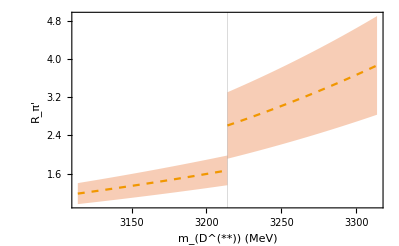

```mathematica
Show[plt1,plt2,PlotRange->All,GridLines->{{3214},None},FrameLabel->{"m_(D^(**)) (MeV)", "R_π'"},PlotLabels->{"A","B"}]
```